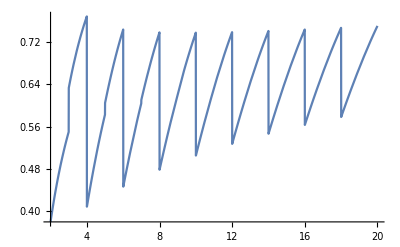

```mathematica
(* https://www.expii.com/solve/40/4 *)
(* Collaboration is very powerful! Suppose you have a group of F students,each of whom independently has 55% chance of correctly answering each true/false question on a test with 25 questions. Unfortunately, unlike the first puzzle, this time they don’t know whether they know or do not know each answer. What is the minimum number of students which is sufficient to collaborate on the test,so that there is a strategy which results in them achieving an A (at least 90% answers correct) with probability at least half? *)

(* Probability that for n students, more than half the students are correct for a single question *)
Clear[p];
(* Sum is for cases n/2+1 students correct, n/2+2 correct and so on ... until n*)
p[n_]:=Sum[Binomial[n,i]0.55^i 0.45^(n-i),{i,Ceiling[n/2],n}]/Sum[ Binomial[n,i]0.55^i 0.45^(n-i),{i,1,n}];
Plot[p[n],{n,2,20}]
```

```mathematica
(* To get an A at least 23 questions have to be right *) 
res[n_]:=Sum[Binomial[25,k] p[n]^k (1-p[n])^(25-k),{k,23,25}];
```

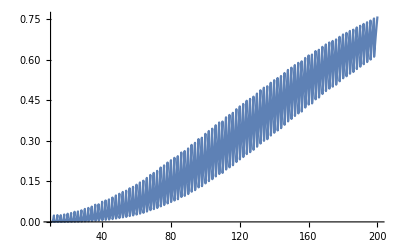

```mathematica
Plot[res[n],{n,10,200}]
```

```mathematica
(* Lowest number n so at least 23 questions are correct with p>0.5 *)
res[157]
```

0.509046